## Initialise

From https://demonstrations.wolfram.com/FiniteDifferenceSchemesOfOneVariable/ 
Took a bit of figuring out, but it writes out finite difference "stencils"

nodenum -- number of nodes (sets accuracy) 
DerNode -- node to vary about; lets you put in "one-sided" difference schemes
 DerOrder -- order of derivative  
 f -- name of the function x

```mathematica
FinDiffScheme[NodeNum_,DerNode_,DerOrder_,f_]:=
Module[{c,cons,dervs,eqn,num,ord,serie,serieCons,system},
cons=Array[c,NodeNum];
eqn=Derivative[DerOrder][f][i]+Map[f,i+(Range[NodeNum]-DerNode)].cons;
dervs=Map[Derivative[#][f][i]&,Range[0,NodeNum+5]];
serie=Expand[eqn//.{f[i+k_]->Normal[Series[f[i+h k],{h,0,NodeNum+5}]], Derivative[d1_][f][i+k_]->D[Normal[Series[f[i+h k],{h,0,NodeNum+5}]],{i,DerOrder}]}];
system=Thread[Map[Coefficient[Collect[serie,dervs],#]&,dervs]==0];
num=NodeNum;
While[Length[First[Solve[Take[system,num],cons]]]=!=NodeNum,num=num+1];
cons=First[Solve[Take[system,num],cons]];
serieCons=serie/.cons;
ord=If[Length[serieCons]>1,First[serieCons],serieCons];
eqn=Equal@@Simplify[Solve[eqn==0,Derivative[DerOrder][f][i]][[1,1]]/.cons];
(* First[eqn]==HoldForm[Evaluate[Together[ExpandAll[Last[eqn]]]]]+Row[{Style["O",Italic],"(",ord,")"}] *)
ReleaseHold[HoldForm[Evaluate[Together[ExpandAll[Last[eqn]]]]]]
]

FinDiffScheme[NodeNum_,DerNode_,DerOrder_]:=
Module[{c,cons,dervs,eqn,num,ord,serie,serieCons,system},
cons=Array[c,NodeNum];
eqn=Derivative[DerOrder][f][i]+Map[f,i+(Range[NodeNum]-DerNode)].cons;
dervs=Map[Derivative[#][f][i]&,Range[0,NodeNum+5]];
serie=Expand[eqn//.{f[i+k_]->Normal[Series[f[i+h k],{h,0,NodeNum+5}]], Derivative[d1_][f][i+k_]->D[Normal[Series[f[i+h k],{h,0,NodeNum+5}]],{i,DerOrder}]}];
system=Thread[Map[Coefficient[Collect[serie,dervs],#]&,dervs]==0];
num=NodeNum;
While[Length[First[Solve[Take[system,num],cons]]]=!=NodeNum,num=num+1];
cons=First[Solve[Take[system,num],cons]];
serieCons=serie/.cons;
ord=If[Length[serieCons]>1,First[serieCons],serieCons];
eqn=Equal@@Simplify[Solve[eqn==0,Derivative[DerOrder][f][i]][[1,1]]/.cons];
First[eqn]==HoldForm[Evaluate[Together[ExpandAll[Last[eqn]]]]]+Row[{Style["O",Italic],"(",ord,")"}]  
 
]
```

## Do x'' + x = 0 as a warm - up

```mathematica
Clear[h]
div2middle  = FinDiffScheme[3,2,2][[2,1,1]]  //. {f[x_]->Subscript[f, x]  } // Simplify
div2left  = FinDiffScheme[3,1,2][[2,1,1]]  //. {f[x_]->Subscript[f, x]  ,i->0} // Simplify
div2right  = FinDiffScheme[3,3,2][[2,1,1]]  //. {f[x_]->Subscript[f, x]  ,i->n} // Simplify
```

(f_(-1+i)-2 f_i+f_(1+i))/h^2

(f_0-2 f_1+f_2)/h^2

(f_(-2+n)-2 f_(-1+n)+f_n)/h^2

```mathematica
nval = 200  ;(* number of points *)
hval = 4 Pi /nval  ;(* this will be two periods  *)

(* this a "test" function which tends to zero if the Subscript[f, i] solve our equation, and it is positive definite; the Subscript[f, 0] and Subscript[f, nval] assignments fix the boundary conditions  *)

(* the structure of this term has a "left difference" and "right difference" at each end *)
testterm =(div2left +  Subscript[f, 0])^2    + Sum[(div2middle +  Subscript[f, i])^2,{i,1,nval-1}]  + (div2right +  Subscript[f, nval])^2  //.  {h-> hval , fun-> f,Subscript[f, 0]-> 1,n->nval, Subscript[f, nval]-> 1} ;
```

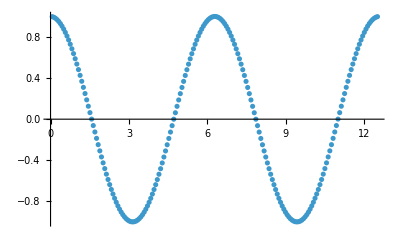

```mathematica
work2 = FindMinimum[testterm ,Table[{Subscript[f, i],1},{i,1,nval-1}]];
results = Table[{i hval ,Subscript[f, i]},{i,0,nval} ]/. work2[[2]] ;


ListPlot[results]
```

## Now we solve the soliton profile

The equations below generate a finite difference approximation to the  f and Φ equations for the soliton profile; they are designed to keep them “in domain” so they become increasingly “one sided” at the endpoints. 

The apparent singularity at the origin is avoided, since the f’ term is omitted at i=0. More complicated potentials should be relatively easy  to add.

```mathematica
termf[ival_,n_,order_] := Which[ival==0, (-FinDiffScheme[order,1,2,f]/2     + f[ival]ϕ[ival] + λint f[ival]^3 ) (* enforces f'[0]=0 *) , 

              ival <=  order/2 ,(-FinDiffScheme[ order,ival+1,2,f]/2  - FinDiffScheme[ order,ival+1,1,f] /(ival h)   + f[ival]ϕ[ival]  + λint f[ival]^3)  ,

order/2 < ival < n-order/2,(-FinDiffScheme[ order,Floor[order/2]+1,2,f]/2  - FinDiffScheme[ order,Floor[order/2]+1,1,f] /(ival h)   + f[ival]ϕ[ival]+ λint f[ival]^3) ,

 n-order/2  <= ival, 
(-FinDiffScheme[ order,order-n+ival,2,f]/2  - FinDiffScheme[ order,order-n+ival,1,f] /(ival h)   + f[ival]ϕ[ival] + λint f[ival]^3)  
 ] //. {i-> ival  }

termphi[ival_,n_,order_] := Which[ival==0, (FinDiffScheme[order,1,2,ϕ]     -4 Pi f[ival]^2  ) (* enforces f'[0]=0 *) , 
              ival <=  order/2 ,(FinDiffScheme[ order,ival+1,2,ϕ]   + 2  FinDiffScheme[ order,ival+1,1,ϕ] /(ival h)   -4 Pi f[ival]^2    ) ,

order/2 < ival < n-order/2,(FinDiffScheme[ order,Floor[order/2]+1,2,ϕ]   + 2 FinDiffScheme[ order,Floor[order/2]+1,1,ϕ] /(ival h)   -4 Pi f[ival]^2   ) ,

 n-order/2  <= ival, 
(FinDiffScheme[ order,order-n+ival,2,ϕ] +   2 FinDiffScheme[ order,order-n+ival,1,ϕ] /(ival h)   -4 Pi f[ival]^2   )  
 ] //. {i-> ival  }
```

The “test” term is the sum of squares of the “errors” -- the differenced terms would be zero for a solution in the continuum limit; we want to minimise the resulting sum of squares.

```mathematica
testtermsoliton[nval_,rmax_,λ_  ,order_]:= Table[(termphi[j, nval,order]^2  +termf[j, nval,order]^2),{j,0,nval}] //.  {f[x_]-> Subscript[f, x], ϕ[x_]-> Subscript[ϕ, x] ,Subscript[f, 0] -> 1,h-> rmax/nval,λint -> λ ,Subscript[f, nval] -> 0}
```

The actual solver is below; right now it is taking a crude guess at the initial form.   
	nval - number of points 
	rmax - width of “domain” 
	λ - value of quartic coupling (just in the S-P equation as currently set up) 
	order -- order of the finite differencing; seems to be happy with 9
	
Note we have “baked in” some knowledge -- ϕ is strictly increasing and f>0

```mathematica
solfinder[nval_,rmax_,λ_  ,order_] := FindMinimum[Flatten[{Total[testtermsoliton[nval,rmax,λ,order]] ,Table[Subscript[f, i]>0,{i,1,nval-1}], Table[Subscript[ϕ, i+1]>Subscript[ϕ, i],{i,0,nval-1}]}],Join[Table[{Subscript[f, i],Exp[-i/4]},{i,1,nval-1}],Table[{Subscript[ϕ, i],-1},{i,0,nval}]],MaxIterations->1000];
```

Demonstration output... First term is the “error” -- should ideally be zero; trying with λ =20

```mathematica
work2 = solfinder[500,10,20,9]
```

{0.0105757,{f_1→1.,f_2→0.999942,f_3→0.999838,f_4→0.999691,f_5→0.999503,f_6→0.999272,f_7→0.998999,f_8→0.998684,f_9→0.998327,f_10→0.997929,f_11→0.997488,f_12→0.997005,f_13→0.99648,f_14→0.995914,f_15→0.995305,f_16→0.994655,f_17→0.993963,f_18→0.993229,f_19→0.992453,f_20→0.991635,f_21→0.990775,f_22→0.989874,f_23→0.98893,f_24→0.987946,f_25→0.986919,f_26→0.98585,f_27→0.98474,f_28→0.983589,f_29→0.982395,f_30→0.98116,f_31→0.979884,f_32→0.978566,f_33→0.977206,f_34→0.975805,f_35→0.974363,f_36→0.972879,f_37→0.971353,f_38→0.969787,f_39→0.968179,f_40→0.966529,f_41→0.964838,f_42→0.963107,f_43→0.961333,f_44→0.959519,f_45→0.957664,f_46→0.955767,f_47→0.95383,f_48→0.951851,f_49→0.949832,f_50→0.947771,f_51→0.945669,f_52→0.943527,f_53→0.941344,f_54→0.93912,f_55→0.936855,f_56→0.93455,f_57→0.932203,f_58→0.929816,f_59→0.927389,f_60→0.924921,f_61→0.922412,f_62→0.919863,f_63→0.917273,f_64→0.914643,f_65→0.911972,f_66→0.909261,f_67→0.90651,f_68→0.903718,f_69→0.900886,f_70→0.898014,f_71→0.895101,f_72→0.892148,f_73→0.889155,f_74→0.886122,f_75→0.883049,f_76→0.879935,f_77→0.876781,f_78→0.873588,f_79→0.870354,f_80→0.86708,f_81→0.863766,f_82→0.860412,f_83→0.857018,f_84→0.853583,f_85→0.850109,f_86→0.846595,f_87→0.84304,f_88→0.839445,f_89→0.83581,f_90→0.832135,f_91→0.82842,f_92→0.824665,f_93→0.820869,f_94→0.817033,f_95→0.813157,f_96→0.80924,f_97→0.805282,f_98→0.801285,f_99→0.797246,f_100→0.793167,f_101→0.789046,f_102→0.784885,f_103→0.780683,f_104→0.77644,f_105→0.772155,f_106→0.767828,f_107→0.76346,f_108→0.759051,f_109→0.754599,f_110→0.750105,f_111→0.745568,f_112→0.740989,f_113→0.736367,f_114→0.731702,f_115→0.726993,f_116→0.722241,f_117→0.717444,f_118→0.712603,f_119→0.707718,f_120→0.702787,f_121→0.697811,f_122→0.692789,f_123→0.68772,f_124→0.682605,f_125→0.677442,f_126→0.672232,f_127→0.666973,f_128→0.661666,f_129→0.656309,f_130→0.650902,f_131→0.645445,f_132→0.639936,f_133→0.634376,f_134→0.628763,f_135→0.623097,f_136→0.617378,f_137→0.611604,f_138→0.605774,f_139→0.59989,f_140→0.593948,f_141→0.58795,f_142→0.581894,f_143→0.575779,f_144→0.569605,f_145→0.563372,f_146→0.557078,f_147→0.550724,f_148→0.544309,f_149→0.537832,f_150→0.531293,f_151→0.524692,f_152→0.518029,f_153→0.511303,f_154→0.504516,f_155→0.497666,f_156→0.490754,f_157→0.483781,f_158→0.476747,f_159→0.469653,f_160→0.462501,f_161→0.45529,f_162→0.448023,f_163→0.440701,f_164→0.433326,f_165→0.425899,f_166→0.418424,f_167→0.410903,f_168→0.403338,f_169→0.395733,f_170→0.38809,f_171→0.380414,f_172→0.372708,f_173→0.364976,f_174→0.357223,f_175→0.349453,f_176→0.341671,f_177→0.333883,f_178→0.326093,f_179→0.318306,f_180→0.31053,f_181→0.302769,f_182→0.295029,f_183→0.287317,f_184→0.279639,f_185→0.272001,f_186→0.264409,f_187→0.25687,f_188→0.24939,f_189→0.241975,f_190→0.234632,f_191→0.227367,f_192→0.220186,f_193→0.213094,f_194→0.206097,f_195→0.199201,f_196→0.19241,f_197→0.185731,f_198→0.179166,f_199→0.172722,f_200→0.166402,f_201→0.160209,f_202→0.154147,f_203→0.14822,f_204→0.142429,f_205→0.136777,f_206→0.131267,f_207→0.1259,f_208→0.120677,f_209→0.115599,f_210→0.110666,f_211→0.10588,f_212→0.10124,f_213→0.0967454,f_214→0.0923958,f_215→0.0881903,f_216→0.0841276,f_217→0.0802064,f_218→0.0764249,f_219→0.0727813,f_220→0.0692734,f_221→0.0658989,f_222→0.0626555,f_223→0.0595404,f_224→0.0565509,f_225→0.0536843,f_226→0.0509374,f_227→0.0483074,f_228→0.045791,f_229→0.0433851,f_230→0.0410864,f_231→0.0388918,f_232→0.036798,f_233→0.0348017,f_234→0.0328996,f_235→0.0310884,f_236→0.029365,f_237→0.0277262,f_238→0.0261687,f_239→0.0246895,f_240→0.0232854,f_241→0.0219535,f_242→0.0206909,f_243→0.0194945,f_244→0.0183617,f_245→0.0172896,f_246→0.0162756,f_247→0.015317,f_248→0.0144115,f_249→0.0135564,f_250→0.0127494,f_251→0.0119883,f_252→0.0112709,f_253→0.0105949,f_254→0.00995846,f_255→0.00935945,f_256→0.00879603,f_257→0.00826637,f_258→0.00776873,f_259→0.00730142,f_260→0.00686284,f_261→0.00645146,f_262→0.0060658,f_263→0.00570446,f_264→0.0053661,f_265→0.00504945,f_266→0.00475327,f_267→0.00447642,f_268→0.00421778,f_269→0.0039763,f_270→0.00375098,f_271→0.00354086,f_272→0.00334504,f_273→0.00316266,f_274→0.00299291,f_275→0.00283501,f_276→0.00268822,f_277→0.00255185,f_278→0.00242524,f_279→0.00230776,f_280→0.00219884,f_281→0.00209789,f_282→0.00200441,f_283→0.00191789,f_284→0.00183786,f_285→0.00176388,f_286→0.00169552,f_287→0.0016324,f_288→0.00157414,f_289→0.00152039,f_290→0.00147083,f_291→0.00142514,f_292→0.00138305,f_293→0.00134427,f_294→0.00130856,f_295→0.00127567,f_296→0.0012454,f_297→0.00121752,f_298→0.00119185,f_299→0.00116821,f_300→0.00114643,f_301→0.00112636,f_302→0.00110786,f_303→0.00109078,f_304→0.00107501,f_305→0.00106043,f_306→0.00104694,f_307→0.00103445,f_308→0.00102285,f_309→0.00101207,f_310→0.00100204,f_311→0.000992676,f_312→0.000983928,f_313→0.000975733,f_314→0.000968039,f_315→0.000960796,f_316→0.000953962,f_317→0.000947496,f_318→0.000941362,f_319→0.000935527,f_320→0.000929961,f_321→0.000924639,f_322→0.000919534,f_323→0.000914626,f_324→0.000909895,f_325→0.000905323,f_326→0.000900894,f_327→0.000896596,f_328→0.000892414,f_329→0.000888338,f_330→0.000884358,f_331→0.000880465,f_332→0.000876651,f_333→0.00087291,f_334→0.000869235,f_335→0.000865622,f_336→0.000862065,f_337→0.00085856,f_338→0.000855105,f_339→0.000851695,f_340→0.000848328,f_341→0.000845002,f_342→0.000841716,f_343→0.000838466,f_344→0.000835253,f_345→0.000832074,f_346→0.000828928,f_347→0.000825815,f_348→0.000822734,f_349→0.000819684,f_350→0.000816665,f_351→0.000813676,f_352→0.000810717,f_353→0.000807788,f_354→0.000804888,f_355→0.000802016,f_356→0.000799174,f_357→0.00079636,f_358→0.000793575,f_359→0.000790817,f_360→0.000788088,f_361→0.000785387,f_362→0.000782713,f_363→0.000780067,f_364→0.000777448,f_365→0.000774857,f_366→0.000772292,f_367→0.000769754,f_368→0.000767244,f_369→0.000764759,f_370→0.000762301,f_371→0.000759869,f_372→0.000757462,f_373→0.000755082,f_374→0.000752726,f_375→0.000750396,f_376→0.00074809,f_377→0.000745809,f_378→0.000743553,f_379→0.000741321,f_380→0.000739112,f_381→0.000736927,f_382→0.000734765,f_383→0.000732626,f_384→0.00073051,f_385→0.000728416,f_386→0.000726345,f_387→0.000724295,f_388→0.000722267,f_389→0.00072026,f_390→0.000718274,f_391→0.000716309,f_392→0.000714365,f_393→0.000712441,f_394→0.000710536,f_395→0.000708652,f_396→0.000706787,f_397→0.000704941,f_398→0.000703113,f_399→0.000701305,f_400→0.000699515,f_401→0.000697744,f_402→0.00069599,f_403→0.000694254,f_404→0.000692536,f_405→0.000690835,f_406→0.000689151,f_407→0.000687484,f_408→0.000685833,f_409→0.0006842,f_410→0.000682583,f_411→0.000680982,f_412→0.000679397,f_413→0.000677828,f_414→0.000676274,f_415→0.000674737,f_416→0.000673215,f_417→0.000671708,f_418→0.000670216,f_419→0.00066874,f_420→0.000667279,f_421→0.000665832,f_422→0.000664401,f_423→0.000662984,f_424→0.000661581,f_425→0.000660194,f_426→0.00065882,f_427→0.000657461,f_428→0.000656117,f_429→0.000654786,f_430→0.000653469,f_431→0.000652167,f_432→0.000650877,f_433→0.000649601,f_434→0.000648339,f_435→0.000647089,f_436→0.000645852,f_437→0.000644627,f_438→0.000643413,f_439→0.000642211,f_440→0.000641019,f_441→0.000639836,f_442→0.000638663,f_443→0.000637496,f_444→0.000636337,f_445→0.000635181,f_446→0.000634029,f_447→0.000632878,f_448→0.000631726,f_449→0.00063057,f_450→0.000629406,f_451→0.000628232,f_452→0.000627043,f_453→0.000625835,f_454→0.000624601,f_455→0.000623337,f_456→0.000622035,f_457→0.000620686,f_458→0.000619284,f_459→0.000617816,f_460→0.000616272,f_461→0.000614639,f_462→0.000612903,f_463→0.000611048,f_464→0.000609054,f_465→0.000606903,f_466→0.000604572,f_467→0.000602035,f_468→0.000599264,f_469→0.000596229,f_470→0.000592895,f_471→0.000589224,f_472→0.000585174,f_473→0.000580699,f_474→0.000575749,f_475→0.000570267,f_476→0.000564193,f_477→0.000557461,f_478→0.000549997,f_479→0.000541725,f_480→0.000532559,f_481→0.000522408,f_482→0.000511174,f_483→0.000498753,f_484→0.000485034,f_485→0.0004699,f_486→0.000453229,f_487→0.000434892,f_488→0.000414761,f_489→0.000392702,f_490→0.000368585,f_491→0.000342284,f_492→0.000313684,f_493→0.000282683,f_494→0.000249206,f_495→0.000213205,f_496→0.000174745,f_497→0.000133842,f_498→0.0000907467,f_499→0.0000459384,ϕ_0→-20.1576,ϕ_1→-20.1576,ϕ_2→-20.1552,ϕ_3→-20.1511,ϕ_4→-20.1452,ϕ_5→-20.1377,ϕ_6→-20.1285,ϕ_7→-20.1176,ϕ_8→-20.1051,ϕ_9→-20.0908,ϕ_10→-20.075,ϕ_11→-20.0574,ϕ_12→-20.0382,ϕ_13→-20.0174,ϕ_14→-19.9948,ϕ_15→-19.9707,ϕ_16→-19.9449,ϕ_17→-19.9174,ϕ_18→-19.8883,ϕ_19→-19.8576,ϕ_20→-19.8252,ϕ_21→-19.7912,ϕ_22→-19.7556,ϕ_23→-19.7184,ϕ_24→-19.6796,ϕ_25→-19.6391,ϕ_26→-19.5971,ϕ_27→-19.5535,ϕ_28→-19.5083,ϕ_29→-19.4615,ϕ_30→-19.4131,ϕ_31→-19.3632,ϕ_32→-19.3117,ϕ_33→-19.2587,ϕ_34→-19.2042,ϕ_35→-19.1481,ϕ_36→-19.0905,ϕ_37→-19.0313,ϕ_38→-18.9707,ϕ_39→-18.9086,ϕ_40→-18.8449,ϕ_41→-18.7798,ϕ_42→-18.7133,ϕ_43→-18.6453,ϕ_44→-18.5758,ϕ_45→-18.5049,ϕ_46→-18.4325,ϕ_47→-18.3588,ϕ_48→-18.2836,ϕ_49→-18.2071,ϕ_50→-18.1292,ϕ_51→-18.0499,ϕ_52→-17.9692,ϕ_53→-17.8872,ϕ_54→-17.8038,ϕ_55→-17.7192,ϕ_56→-17.6332,ϕ_57→-17.5459,ϕ_58→-17.4574,ϕ_59→-17.3676,ϕ_60→-17.2765,ϕ_61→-17.1842,ϕ_62→-17.0906,ϕ_63→-16.9958,ϕ_64→-16.8999,ϕ_65→-16.8027,ϕ_66→-16.7044,ϕ_67→-16.6049,ϕ_68→-16.5043,ϕ_69→-16.4025,ϕ_70→-16.2996,ϕ_71→-16.1957,ϕ_72→-16.0906,ϕ_73→-15.9845,ϕ_74→-15.8773,ϕ_75→-15.7691,ϕ_76→-15.6599,ϕ_77→-15.5496,ϕ_78→-15.4384,ϕ_79→-15.3262,ϕ_80→-15.2131,ϕ_81→-15.099,ϕ_82→-14.984,ϕ_83→-14.868,ϕ_84→-14.7512,ϕ_85→-14.6336,ϕ_86→-14.515,ϕ_87→-14.3957,ϕ_88→-14.2755,ϕ_89→-14.1545,ϕ_90→-14.0327,ϕ_91→-13.9102,ϕ_92→-13.7869,ϕ_93→-13.6629,ϕ_94→-13.5382,ϕ_95→-13.4128,ϕ_96→-13.2867,ϕ_97→-13.1599,ϕ_98→-13.0325,ϕ_99→-12.9045,ϕ_100→-12.7759,ϕ_101→-12.6467,ϕ_102→-12.5169,ϕ_103→-12.3866,ϕ_104→-12.2558,ϕ_105→-12.1244,ϕ_106→-11.9926,ϕ_107→-11.8603,ϕ_108→-11.7275,ϕ_109→-11.5943,ϕ_110→-11.4607,ϕ_111→-11.3267,ϕ_112→-11.1923,ϕ_113→-11.0576,ϕ_114→-10.9225,ϕ_115→-10.7871,ϕ_116→-10.6514,ϕ_117→-10.5154,ϕ_118→-10.3792,ϕ_119→-10.2427,ϕ_120→-10.106,ϕ_121→-9.96909,ϕ_122→-9.83201,ϕ_123→-9.69476,ϕ_124→-9.55736,ϕ_125→-9.41984,ϕ_126→-9.28222,ϕ_127→-9.14451,ϕ_128→-9.00673,ϕ_129→-8.86891,ϕ_130→-8.73105,ϕ_131→-8.59319,ϕ_132→-8.45534,ϕ_133→-8.31752,ϕ_134→-8.17975,ϕ_135→-8.04205,ϕ_136→-7.90443,ϕ_137→-7.76692,ϕ_138→-7.62954,ϕ_139→-7.49231,ϕ_140→-7.35523,ϕ_141→-7.21835,ϕ_142→-7.08166,ϕ_143→-6.9452,ϕ_144→-6.80898,ϕ_145→-6.67301,ϕ_146→-6.53733,ϕ_147→-6.40194,ϕ_148→-6.26686,ϕ_149→-6.13212,ϕ_150→-5.99774,ϕ_151→-5.86372,ϕ_152→-5.73009,ϕ_153→-5.59687,ϕ_154→-5.46408,ϕ_155→-5.33172,ϕ_156→-5.19983,ϕ_157→-5.06841,ϕ_158→-4.93749,ϕ_159→-4.80708,ϕ_160→-4.67719,ϕ_161→-4.54786,ϕ_162→-4.41908,ϕ_163→-4.29088,ϕ_164→-4.16327,ϕ_165→-4.03628,ϕ_166→-3.9099,ϕ_167→-3.78417,ϕ_168→-3.65909,ϕ_169→-3.53467,ϕ_170→-3.41094,ϕ_171→-3.2879,ϕ_172→-3.16557,ϕ_173→-3.04396,ϕ_174→-2.92308,ϕ_175→-2.80295,ϕ_176→-2.68357,ϕ_177→-2.56495,ϕ_178→-2.44711,ϕ_179→-2.33006,ϕ_180→-2.2138,ϕ_181→-2.09834,ϕ_182→-1.98369,ϕ_183→-1.86986,ϕ_184→-1.75686,ϕ_185→-1.64468,ϕ_186→-1.53335,ϕ_187→-1.42285,ϕ_188→-1.3132,ϕ_189→-1.2044,ϕ_190→-1.09645,ϕ_191→-0.989354,ϕ_192→-0.883117,ϕ_193→-0.777738,ϕ_194→-0.673219,ϕ_195→-0.569559,ϕ_196→-0.466758,ϕ_197→-0.364816,ϕ_198→-0.263731,ϕ_199→-0.163501,ϕ_200→-0.0641244,ϕ_201→0.034402,ϕ_202→0.132081,ϕ_203→0.228917,ϕ_204→0.324913,ϕ_205→0.420075,ϕ_206→0.514406,ϕ_207→0.607911,ϕ_208→0.700597,ϕ_209→0.792469,ϕ_210→0.883533,ϕ_211→0.973795,ϕ_212→1.06326,ϕ_213→1.15194,ϕ_214→1.23984,ϕ_215→1.32696,ϕ_216→1.41331,ϕ_217→1.4989,ϕ_218→1.58374,ϕ_219→1.66784,ϕ_220→1.75119,ϕ_221→1.83382,ϕ_222→1.91572,ϕ_223→1.99691,ϕ_224→2.07739,ϕ_225→2.15717,ϕ_226→2.23626,ϕ_227→2.31467,ϕ_228→2.3924,ϕ_229→2.46946,ϕ_230→2.54586,ϕ_231→2.62161,ϕ_232→2.69671,ϕ_233→2.77118,ϕ_234→2.84501,ϕ_235→2.91823,ϕ_236→2.99082,ϕ_237→3.06281,ϕ_238→3.1342,ϕ_239→3.20499,ϕ_240→3.27519,ϕ_241→3.34482,ϕ_242→3.41387,ϕ_243→3.48236,ϕ_244→3.55029,ϕ_245→3.61766,ϕ_246→3.68449,ϕ_247→3.75078,ϕ_248→3.81653,ϕ_249→3.88176,ϕ_250→3.94647,ϕ_251→4.01066,ϕ_252→4.07434,ϕ_253→4.13752,ϕ_254→4.20021,ϕ_255→4.2624,ϕ_256→4.32411,ϕ_257→4.38533,ϕ_258→4.44609,ϕ_259→4.50637,ϕ_260→4.56619,ϕ_261→4.62555,ϕ_262→4.68446,ϕ_263→4.74293,ϕ_264→4.80094,ϕ_265→4.85853,ϕ_266→4.91567,ϕ_267→4.97239,ϕ_268→5.02869,ϕ_269→5.08457,ϕ_270→5.14004,ϕ_271→5.19509,ϕ_272→5.24974,ϕ_273→5.30399,ϕ_274→5.35785,ϕ_275→5.41131,ϕ_276→5.46439,ϕ_277→5.51708,ϕ_278→5.56939,ϕ_279→5.62133,ϕ_280→5.6729,ϕ_281→5.7241,ϕ_282→5.77494,ϕ_283→5.82541,ϕ_284→5.87554,ϕ_285→5.92531,ϕ_286→5.97473,ϕ_287→6.02381,ϕ_288→6.07255,ϕ_289→6.12095,ϕ_290→6.16901,ϕ_291→6.21675,ϕ_292→6.26416,ϕ_293→6.31125,ϕ_294→6.35801,ϕ_295→6.40446,ϕ_296→6.45059,ϕ_297→6.49642,ϕ_298→6.54193,ϕ_299→6.58715,ϕ_300→6.63206,ϕ_301→6.67667,ϕ_302→6.72099,ϕ_303→6.76501,ϕ_304→6.80874,ϕ_305→6.85219,ϕ_306→6.89536,ϕ_307→6.93824,ϕ_308→6.98084,ϕ_309→7.02317,ϕ_310→7.06523,ϕ_311→7.10701,ϕ_312→7.14853,ϕ_313→7.18978,ϕ_314→7.23077,ϕ_315→7.2715,ϕ_316→7.31197,ϕ_317→7.35218,ϕ_318→7.39215,ϕ_319→7.43186,ϕ_320→7.47132,ϕ_321→7.51054,ϕ_322→7.54951,ϕ_323→7.58825,ϕ_324→7.62674,ϕ_325→7.665,ϕ_326→7.70302,ϕ_327→7.74081,ϕ_328→7.77837,ϕ_329→7.8157,ϕ_330→7.85281,ϕ_331→7.88969,ϕ_332→7.92635,ϕ_333→7.96278,ϕ_334→7.999,ϕ_335→8.03501,ϕ_336→8.0708,ϕ_337→8.10638,ϕ_338→8.14174,ϕ_339→8.1769,ϕ_340→8.21185,ϕ_341→8.2466,ϕ_342→8.28114,ϕ_343→8.31548,ϕ_344→8.34962,ϕ_345→8.38357,ϕ_346→8.41732,ϕ_347→8.45087,ϕ_348→8.48423,ϕ_349→8.5174,ϕ_350→8.55038,ϕ_351→8.58317,ϕ_352→8.61578,ϕ_353→8.6482,ϕ_354→8.68044,ϕ_355→8.71249,ϕ_356→8.74437,ϕ_357→8.77607,ϕ_358→8.80759,ϕ_359→8.83893,ϕ_360→8.8701,ϕ_361→8.9011,ϕ_362→8.93193,ϕ_363→8.96258,ϕ_364→8.99307,ϕ_365→9.02339,ϕ_366→9.05355,ϕ_367→9.08354,ϕ_368→9.11337,ϕ_369→9.14303,ϕ_370→9.17254,ϕ_371→9.20189,ϕ_372→9.23108,ϕ_373→9.26011,ϕ_374→9.28899,ϕ_375→9.31771,ϕ_376→9.34628,ϕ_377→9.3747,ϕ_378→9.40297,ϕ_379→9.43109,ϕ_380→9.45906,ϕ_381→9.48689,ϕ_382→9.51457,ϕ_383→9.5421,ϕ_384→9.56949,ϕ_385→9.59674,ϕ_386→9.62385,ϕ_387→9.65082,ϕ_388→9.67765,ϕ_389→9.70434,ϕ_390→9.73089,ϕ_391→9.75731,ϕ_392→9.78359,ϕ_393→9.80974,ϕ_394→9.83576,ϕ_395→9.86164,ϕ_396→9.8874,ϕ_397→9.91302,ϕ_398→9.93852,ϕ_399→9.96389,ϕ_400→9.98913,ϕ_401→10.0142,ϕ_402→10.0392,ϕ_403→10.0641,ϕ_404→10.0888,ϕ_405→10.1135,ϕ_406→10.138,ϕ_407→10.1623,ϕ_408→10.1866,ϕ_409→10.2107,ϕ_410→10.2348,ϕ_411→10.2587,ϕ_412→10.2825,ϕ_413→10.3061,ϕ_414→10.3297,ϕ_415→10.3532,ϕ_416→10.3765,ϕ_417→10.3997,ϕ_418→10.4228,ϕ_419→10.4458,ϕ_420→10.4687,ϕ_421→10.4915,ϕ_422→10.5142,ϕ_423→10.5367,ϕ_424→10.5592,ϕ_425→10.5816,ϕ_426→10.6038,ϕ_427→10.626,ϕ_428→10.648,ϕ_429→10.6699,ϕ_430→10.6918,ϕ_431→10.7135,ϕ_432→10.7352,ϕ_433→10.7567,ϕ_434→10.7781,ϕ_435→10.7995,ϕ_436→10.8207,ϕ_437→10.8418,ϕ_438→10.8629,ϕ_439→10.8838,ϕ_440→10.9047,ϕ_441→10.9255,ϕ_442→10.9461,ϕ_443→10.9667,ϕ_444→10.9872,ϕ_445→11.0076,ϕ_446→11.0279,ϕ_447→11.0481,ϕ_448→11.0682,ϕ_449→11.0882,ϕ_450→11.1082,ϕ_451→11.128,ϕ_452→11.1478,ϕ_453→11.1674,ϕ_454→11.187,ϕ_455→11.2065,ϕ_456→11.226,ϕ_457→11.2453,ϕ_458→11.2645,ϕ_459→11.2837,ϕ_460→11.3028,ϕ_461→11.3218,ϕ_462→11.3407,ϕ_463→11.3595,ϕ_464→11.3783,ϕ_465→11.3969,ϕ_466→11.4155,ϕ_467→11.4341,ϕ_468→11.4525,ϕ_469→11.4708,ϕ_470→11.4891,ϕ_471→11.5073,ϕ_472→11.5254,ϕ_473→11.5435,ϕ_474→11.5614,ϕ_475→11.5793,ϕ_476→11.5972,ϕ_477→11.6149,ϕ_478→11.6326,ϕ_479→11.6502,ϕ_480→11.6677,ϕ_481→11.6851,ϕ_482→11.7025,ϕ_483→11.7198,ϕ_484→11.737,ϕ_485→11.7542,ϕ_486→11.7713,ϕ_487→11.7883,ϕ_488→11.8053,ϕ_489→11.8222,ϕ_490→11.839,ϕ_491→11.8557,ϕ_492→11.8724,ϕ_493→11.889,ϕ_494→11.9055,ϕ_495→11.922,ϕ_496→11.9384,ϕ_497→11.9548,ϕ_498→11.971,ϕ_499→11.9872,ϕ_500→12.0034}}

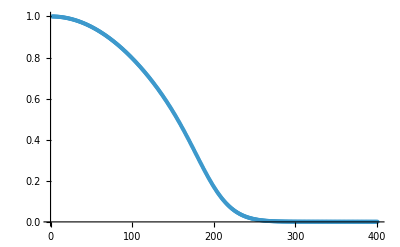

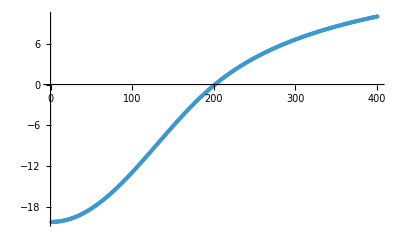

```mathematica
fpoints =Table[Subscript[f, i],{i,0,400} ]/. work2[[2]] ;
phipoints =Table[Subscript[ϕ, i],{i,0,400} ]/. work2[[2]] ;

ListPlot[fpoints ,PlotRange->All]
ListPlot[phipoints]
```